```mathematica
f[x_,y_]:=Sin[x];  (* Reals^2 -> Reals *)
Plot3D[f[x,y], {x, 0, 2 Pi}, {y, 0 , 2 Pi}, AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
f[x_,y_]:=Exp[x];   (* Reals^2 -> Reals *)
Plot3D[f[x,y], {x, 0, 2 Pi}, {y, 0 , 2 Pi}, AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
f[x_,y_]:=x^2;   (* Reals^2 -> Reals *)
Plot3D[f[x,y], {x, -5,5}, {y,-5,5}, AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
f[x_,y_]:=x^2+y^2;   (* Reals^2 -> Reals *)
Plot3D[f[x,y], {x, -5,5}, {y,-5,5}, AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
f[x_,y_]:=√(x^2+y^2);   (* Reals^2 -> Reals *)
Plot3D[f[x,y], {x, -5,5}, {y,-5,5}, AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
f[x_,y_]:=Sin[√(x^2+y^2)];   (* Reals^2 -> Reals *)
Plot3D[f[x,y], {x, -12,12}, {y,-12,12}, AxesLabel->Automatic]
```

-Graphics3D-

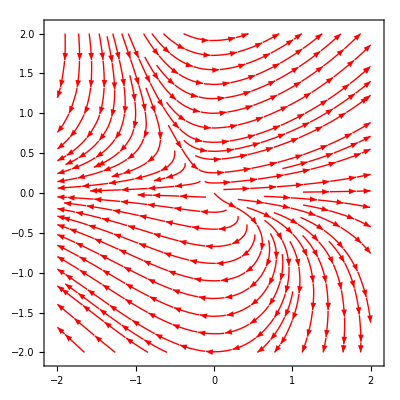

-Graphics-

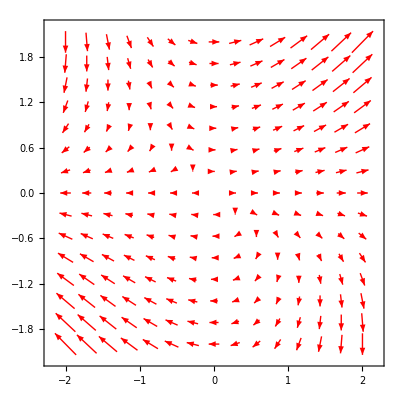

```mathematica
f[x_,y_]:={x+y, x*y};   (* Reals^2 -> Reals^2 *)
StreamPlot[f[x,y],{x,-2,2},{y,-2,2},StreamStyle->Red]
VectorPlot[f[x,y],{x,-2,2},{y,-2,2},VectorStyle->"Arrow3D",VectorScale->{0.03,0.3,None},StreamPoints->Fine]
VectorPlot[f[x,y],{x,-2,2},{y,-2,2},VectorStyle->Red]
```